```mathematica
Exit[]
```

```mathematica
SetDirectory[$HomeDirectory<>"\\My Documents\\Notebooks\\Packages"]
```

C:\Documents and Settings\igloris\My Documents\Notebooks\Packages

Load package for calcuating l1 solution

```mathematica
<<L1Packv2`
```

```mathematica
numvar=100;
numdata=30;
numnonzero=10;
noiselevel=0.03;
```

==============================

Read in the numbers (mat, inputsol, noise)

```mathematica
Get[$HomeDirectory<>"\\My Documents\\Notebooks\\CStoyexample\\example2data"];
```

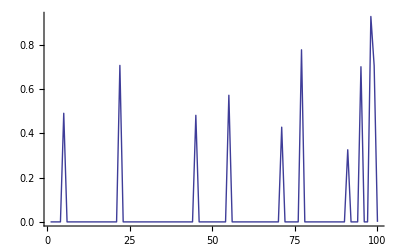

```mathematica
ListPlot[inputsol,Joined->True]
```

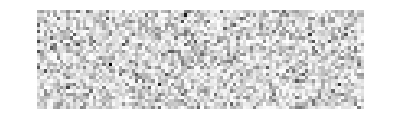

```mathematica
ArrayPlot[mat]
```

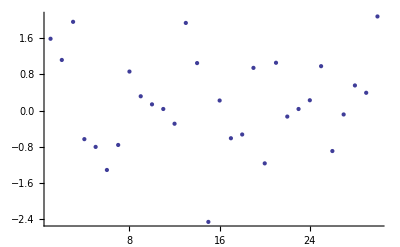

```mathematica
ListPlot[noise]
```

Prepare data :

```mathematica
noiselessdata=mat.inputsol;
```

```mathematica
sigma=noiselevel*Norm[noiselessdata]
```

0.378203

Add noise to data :

```mathematica
data=noiselessdata+noiselevel*Norm[noiselessdata]/Norm[noise]*noise
```

{2.25954,1.82413,-5.05755,2.43719,0.26397,-1.91692,-4.69052,0.581962,0.672173,-0.343035,2.14586,-0.401462,0.244748,3.3135,1.69963,-6.39666,-1.07171,-0.323599,-0.301916,-0.354564,0.348566,-0.441993,-1.12557,-2.24714,-1.56196,3.77354,1.69599,1.68883,0.410689,1.32006}

This is the norm squared of how much noise was added to the noiseless data :

```mathematica
err=Norm[noiselevel*Norm[noiselessdata]/Norm[noise]*noise]^2
```

0.143037

Find l1 solution with exactly this data misfit :

```mathematica
outputsol1=FindMinimizer[mat,data,MinimumDiscrepancy->err];
```

Double check :

```mathematica
Norm[mat.outputsol1-data]^2
```

0.143037

Now calculate l2 solution with the same data fit :

```mathematica
l2penaltyparam=2.504135;(*trial and error*)
outputsol2=LinearSolve[Transpose[mat].mat+l2penaltyparam*IdentityMatrix[100],Transpose[mat].data];
```

Double check :

```mathematica
Norm[mat.outputsol2-data]^2
```

0.143037

Verify that outputsol1 is much closer to inputsol than outputsol2 :

```mathematica
{Norm[inputsol-outputsol1]/Norm[inputsol],Norm[inputsol-outputsol2]/Norm[inputsol]}
```

{0.12582,0.761242}

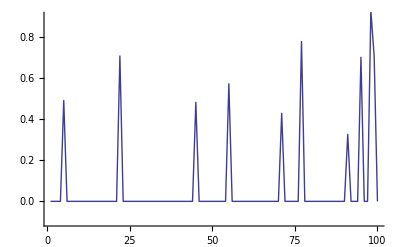

```mathematica
ListPlot[inputsol,Joined->True,PlotRange->{-0.1,0.9}]
```

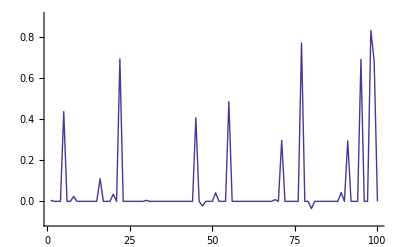

```mathematica
ListPlot[outputsol1,Joined->True,PlotRange->{-0.1,0.9}]
```

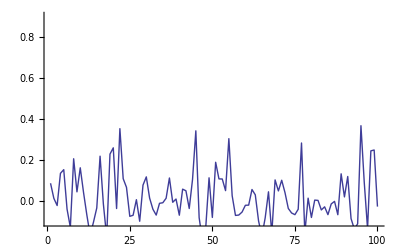

```mathematica
ListPlot[outputsol2,Joined->True,PlotRange->{-0.1,0.9}]
```